## Mobius matrix of graph - not a full one

```mathematica
allGraphs5[K5Key,"colofour"]
```

v1x2x3x4x5

```mathematica
Keys5[colofour_]:=Keys5[colofour]=Select[Keys[allGraphs5],Length[ListofVars[allGraphs5[#,colofour]]]==1&]
```

```mathematica
Vars5[colofour_]:=Vars5[colofour]=Sort[Table[allGraphs5[k,colofour],{k,Keys5[colofour]}],CompareSymbols]
```

```mathematica
MobiusGraph4Colofour[key_,allGraphs_,colofour_]:=Block[{form=allGraphs[key,colofour], vars, blocks=Association[],c,edges,set, found=Association[],realyNullAtomKeys=Keys5[colofour],problemSize=Length[allGraphs[0,"vertexsets"]]},
vars=ListofVars[form];
(* initialize all blocks to empty sets *)
Table[blocks[k]={},{k,0,problemSize}];
(* put each base set ion a bucket by length.  In eahc bucket we store the variable and the vertexsets associated with that variable *)
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,colofour]===v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}
];
(* now compute the edges.
For this we go over all blocks per size.
For each of the "size +1" we add and an edge if the first is a refinement of the second
*)
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],

AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,problemSize}];
Graph[vars,edges,VertexLabels->Table[n->Tooltip[Rotate[(TableForm[{n,Style[Coefficient[form,n],Bold,Blue], Style[DropMore[n,3],Red]},TableAlignments->Center]),Pi/4],found[n,"graph"]],{n,vars}],GraphLayout->"LayeredDigraphEmbedding"]
]
```

```mathematica
allGraphs5[K4Key,"colofournull"]
```

p1x2345

{0,19683,29524,28764,27246,26487,26488,22708,21951,21954,20439,20448,19692,19696,19686,19684,6561,9490,8784,8757,7374,7293,6642,6670,6588,6562,2187,3160,2917,2430,2460,2214,2190,729,972,1062,810,738,243,364,333,273,244,81,109,84,27,36,9,13,3,1}

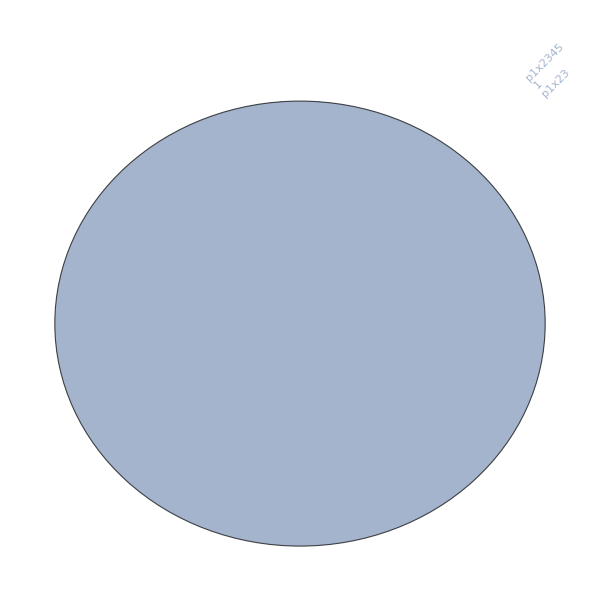

```mathematica
MobiusGraph4Colofour[K4Key,allGraphs5,"colofournull"]
```

```mathematica
PartialMobius[k_,colofour_:"colofourrealnull"]:=Block[{
allPartitions=Vars5[colofour],
result=Association[],
vars=ReverseSort[ ListofVars[allGraphs5[k,colofour]],CompareSymbols],
mobius =Graph[MobiusGraph4Colofour[k,allGraphs5,colofour],ImageSize->Small],
outvertices
},
(* initialize the result.  This is a two dimensional dictionary with partition symbols as keys *)
Table[result[p]=Association[];Table[result[p,p2]=0,{p2,allPartitions}],{p,allPartitions}];

(* all variables that occur have a 1 at the diagonal *)
Table[result[v,v]=1,{v,vars}];
(*Print[vars,mobius];*)

(* now for every var we compute the mobius using the mobius graph *)
vars=Rest[vars];(* head is 0 element of the lattice *)
Table[
outvertices=Select[VertexOutComponent[mobius,v],#=!=v&];
(*outvertices=Select[outvertices,SymbolLevel[#]==SymbolLevel[v]-1&];*)
(*Print[v->outvertices];*)
Table[result[v,p]=-Total[Table[result[v2,p],{v2,outvertices}]],{p,Select[allPartitions,#=!=v&]}];
,
{v,vars}
];

(* compute the result.  Keys that don't exist have value 0 *)
Table[If[!KeyExistsQ[result[p1],p2],0,result[p1,p2]],{p1,allPartitions},{p2,allPartitions}]
]
```

```mathematica
MobiusMatrix[allGraphs5]==PartialMobius[K5Key]
```

True

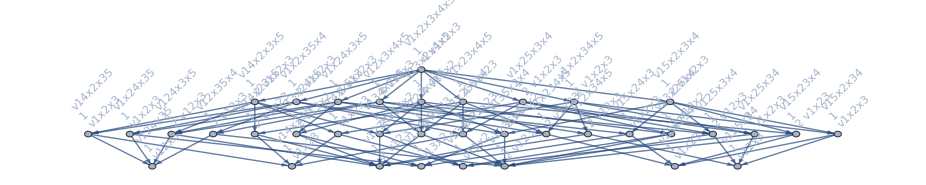
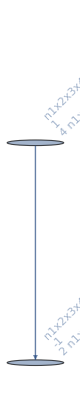
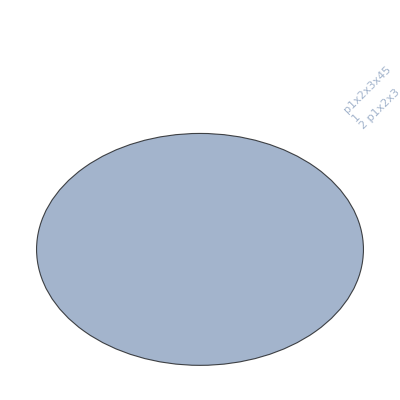
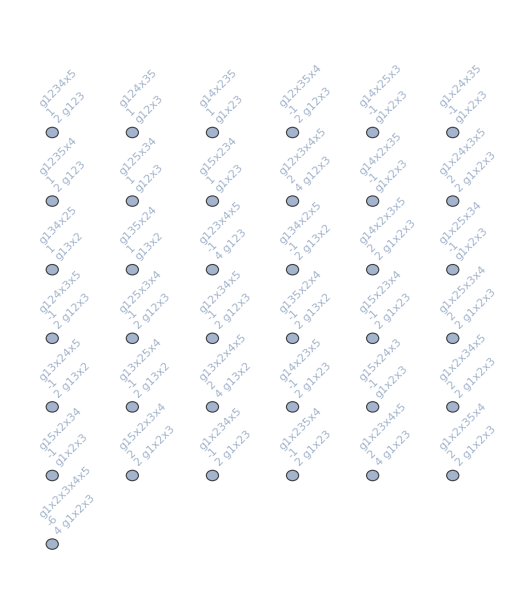
{v1234x5+v1235x4+v123x4x5+v124x35+v124x3x5+v125x34+v125x3x4+v12x34x5+v12x35x4+v12x3x4x5+v134x25+v134x2x5+v135x24+v135x2x4+v13x24x5+v13x25x4+v13x2x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x235x4+v1x23x4x5+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5→-Graphics-,-n1x2x3x45+n1x2x3x4x5→-Graphics-,p1x2x3x45→-Graphics-,g1234x5+g1235x4-g123x4x5+g124x35-g124x3x5+g125x34-g125x3x4-g12x34x5-g12x35x4+2 g12x3x4x5+g134x25-g134x2x5+g135x24-g135x2x4-g13x24x5-g13x25x4+2 g13x2x4x5+g14x235-g14x23x5-g14x25x3-g14x2x35+2 g14x2x3x5+g15x234-g15x23x4-g15x24x3-g15x2x34+2 g15x2x3x4-g1x234x5-g1x235x4+2 g1x23x4x5-g1x24x35+2 g1x24x3x5-g1x25x34+2 g1x25x3x4+2 g1x2x34x5+2 g1x2x35x4-6 g1x2x3x4x5→-Graphics-}

```mathematica
With[
{k=1},
Table[allGraphs5[k,col]->MobiusGraph4Colofour[k,allGraphs5,col],{col,{"colofour","colofourrealnull","colofournull","colofourgenerator"}}]
]
```

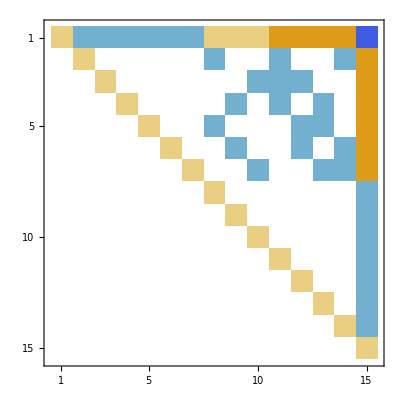

```mathematica
MobiusMatrix[allGraphs4]//MatrixPlot
```

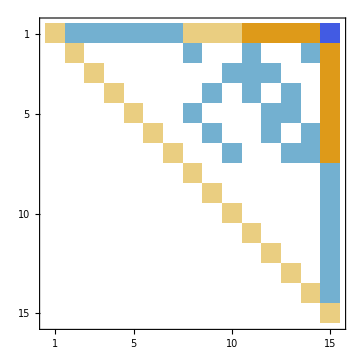

```mathematica
Transpose[Select[Transpose[Select[PartialMobius[K4Key,"colofourrealnull"],#≠Table[0,{k,52}]&]],#≠Table[0,{k,15}]&]]//MatrixPlot
```

```mathematica
ChildMob[k_,colofour_:"colofourrealnul"]:=Labeled[MatrixPlot[PartialMobius[k,colofour]],k]->Table[Table[Labeled[MatrixPlot[PartialMobius[child,colofour]],child],{child,childCouple}],{childCouple,allGraphs5[k,"children"]}]
```

```mathematica
allGraphs5[0,"children"]
```

{{19683,39366},{6561,13122},{2187,4374},{729,1458},{243,486},{81,162},{27,54},{9,18},{3,6},{1,2}}

```mathematica
Solve[PartialMobius[0]==a PartialMobius[19683]+  PartialMobius[39366],{a}]
```

{}

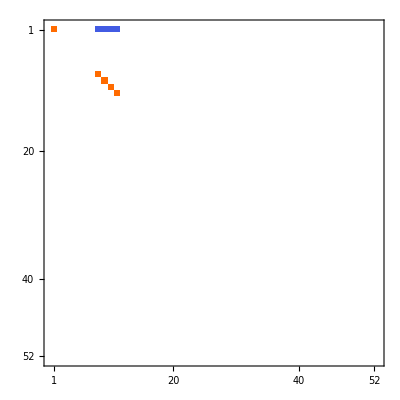
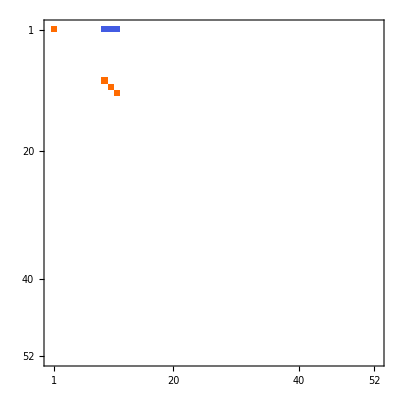
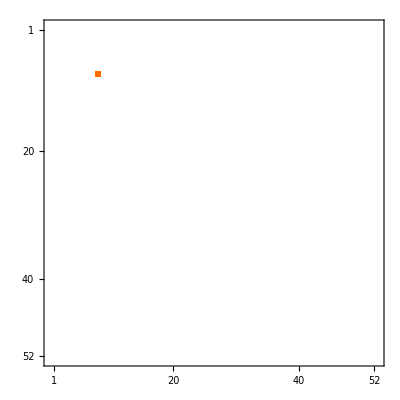
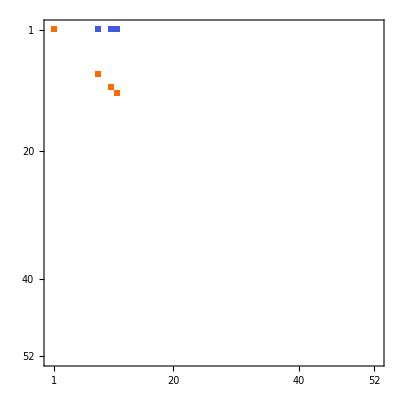
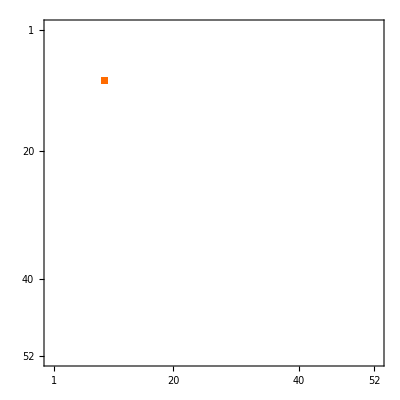
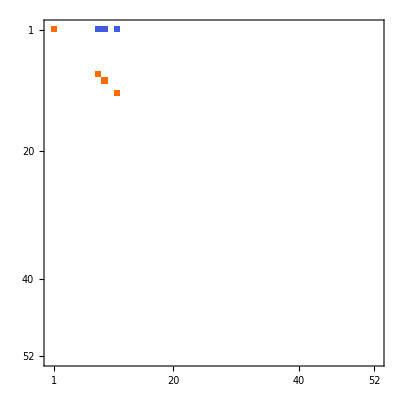
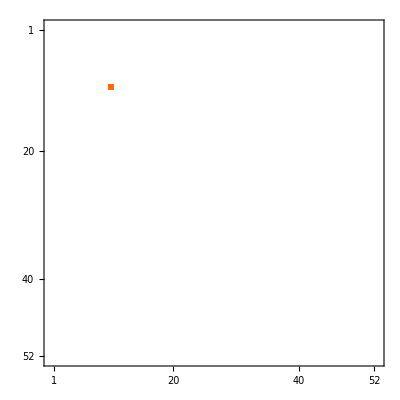
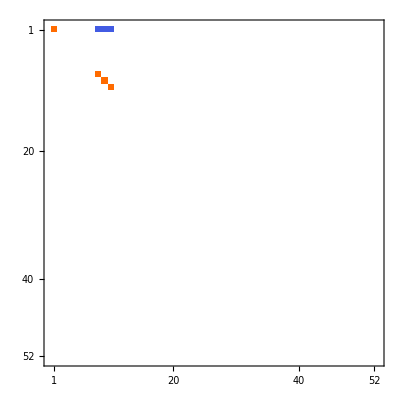
-Graphics-364→{{-Graphics-20047,-Graphics-49207},{-Graphics-6925,-Graphics-36085},{-Graphics-2551,-Graphics-31711},{-Graphics-1093,-Graphics-30253}}

```mathematica
ChildMob[K4Key,"colofour"]
```